#### Задание 22

а) Составить сетевой план комплекса работ. Упорядочить структурную таблицу. 
б) Построить сетевой граф работа-вершина и вершина-событие. 
в) Построить временной сетевой граф: диаграмму Ганта и линейчатый граф. 
г) Построить временной сетевой граф на основе графа вершина-событие и граф с указанием резервов времени. 
д) Найти для всех вариантов временного графа: резерв времени события, ранний срок свершения события, поздний срок свершения события, резерв времени работы, свободный резерв времени работы. 
е) Построить математическую модель получения сетевого плана и реализовать ее.

Структурная таблица

```mathematica
tasks=Sort[{{1,13,{}},{2,5,{}},{3,25,{}},{4,20,{2}},{5,7,{1,6}},{6,3,{7}},{7,4,{2}},{8,6,{3,4,9}},{9,3,{12,13}},{10,10,{7}},{11,22,{7}},{12,14,{5,10}},{13,2,{3,4,14}},{14,12,{5,10}},{15,23,{12,13}}},First];
```

```mathematica
TableForm[tasks,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №"}}]
```

№ | duration | follows №
1 | 13 | {}
2 | 5 | {}
3 | 25 | {}
4 | 20 | {2}
5 | 7 | {1,6}
6 | 3 | {7}
7 | 4 | {2}
8 | 6 | {3,4,9}
9 | 3 | {12,13}
10 | 10 | {7}
11 | 22 | {7}
12 | 14 | {5,10}
13 | 2 | {3,4,14}
14 | 12 | {5,10}
15 | 23 | {12,13}

```mathematica
schedule=Append[#,If[#[[3]]==={},1,Undefined]]&/@tasks;
```

```mathematica
TableForm[schedule,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | Undefined
5 | 7 | {1,6} | Undefined
6 | 3 | {7} | Undefined
7 | 4 | {2} | Undefined
8 | 6 | {3,4,9} | Undefined
9 | 3 | {12,13} | Undefined
10 | 10 | {7} | Undefined
11 | 22 | {7} | Undefined
12 | 14 | {5,10} | Undefined
13 | 2 | {3,4,14} | Undefined
14 | 12 | {5,10} | Undefined
15 | 23 | {12,13} | Undefined

```mathematica
ClearAll[nestWBS];
nestWBS[wbs_List]:=Module[
{},
Table[
ReplacePart[
wbs⟦i⟧,
4->If[
wbs⟦i,4⟧===Undefined,
Max[
Select[
wbs,
MemberQ[wbs⟦i,3⟧,#[[1]]]&
]⟦All,4⟧]+1,
wbs⟦i,4⟧]],
{i,Length@schedule}]
]
```

```mathematica
wbs=NestWhile[nestWBS,schedule,MemberQ[#,Undefined,2]&];
```

```mathematica
TableForm[wbs,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | 2
5 | 7 | {1,6} | 4
6 | 3 | {7} | 3
7 | 4 | {2} | 2
8 | 6 | {3,4,9} | 8
9 | 3 | {12,13} | 7
10 | 10 | {7} | 3
11 | 22 | {7} | 3
12 | 14 | {5,10} | 5
13 | 2 | {3,4,14} | 6
14 | 12 | {5,10} | 5
15 | 23 | {12,13} | 7

```mathematica
sortedWBS=SortBy[wbs,Last];
```

```mathematica
TableForm[sortedWBS,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | 2
7 | 4 | {2} | 2
6 | 3 | {7} | 3
10 | 10 | {7} | 3
11 | 22 | {7} | 3
5 | 7 | {1,6} | 4
12 | 14 | {5,10} | 5
14 | 12 | {5,10} | 5
13 | 2 | {3,4,14} | 6
9 | 3 | {12,13} | 7
15 | 23 | {12,13} | 7
8 | 6 | {3,4,9} | 8

```mathematica
rules=Thread[sortedWBS⟦All,1⟧->Range[Length@sortedWBS]]
```

{1→1,2→2,3→3,4→4,7→5,6→6,10→7,11→8,5→9,12→10,14→11,13→12,9→13,15→14,8→15}

```mathematica
data=Replace[ReplaceAt[sortedWBS,rules,{All,1}],rules,{3}];
```

```mathematica
TableForm[data,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | 2
5 | 4 | {2} | 2
6 | 3 | {5} | 3
7 | 10 | {5} | 3
8 | 22 | {5} | 3
9 | 7 | {1,6} | 4
10 | 14 | {9,7} | 5
11 | 12 | {9,7} | 5
12 | 2 | {3,4,11} | 6
13 | 3 | {10,12} | 7
14 | 23 | {10,12} | 7
15 | 6 | {3,4,13} | 8

Ориентированный граф по исходной таблице (до ранжирования)

```mathematica
edges1=Flatten[Thread/@Thread[DirectedEdge[schedule⟦All,3⟧,schedule⟦All,1⟧]]]
```

{2->4,1->5,6->5,7->6,2->7,3->8,4->8,9->8,12->9,13->9,7->10,7->11,5->12,10->12,3->13,4->13,14->13,5->14,10->14,12->15,13->15}

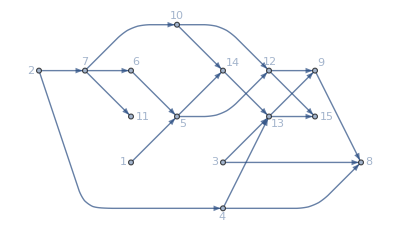

```mathematica
Graph[edges1,VertexLabels->"Name",GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

Ориентированный граф по упорядоченной структурной таблице

```mathematica
edges=Flatten[Thread/@Thread[DirectedEdge[data⟦All,3⟧,data⟦All,1⟧]]]
```

{2->4,2->5,5->6,5->7,5->8,1->9,6->9,9->10,7->10,9->11,7->11,3->12,4->12,11->12,10->13,12->13,10->14,12->14,3->15,4->15,13->15}

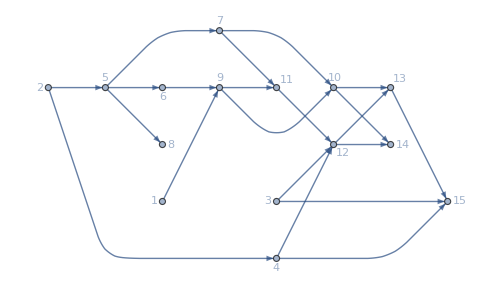

```mathematica
Graph[edges,VertexLabels->"Name",GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

Сетевой граф “работа-вершина”

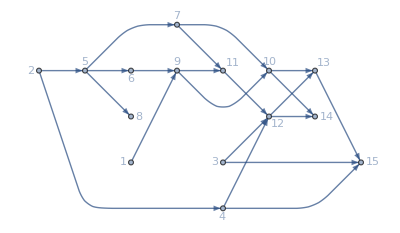

```mathematica
LayeredGraphPlot[edges,Left,VertexLabels->"Name"]
```

```mathematica
ranks=Thread[data⟦All,1⟧->data⟦All,4⟧]
```

{1→1,2→1,3→1,4→2,5→2,6→3,7→3,8→3,9→4,10→5,11→5,12→6,13→7,14→7,15→8}

```mathematica
(*Создаем координаты с равномерным распределением*)
rankGroups=GroupBy[ranks,Last->First];
coordRules=Flatten[Table[rankVertices=rankGroups[rank];
Table[v->{rank,-Position[rankVertices,v][[1,1]]},{v,rankVertices}],{rank,Sort[Keys[rankGroups]]}],1];
```

```mathematica
(*Дуги*)
edgeShapeFunction=Which[
Abs[coordRules[[#2[[1]],1]]-coordRules[[#2[[2]],1]]]>2,
[{"CurvedArc","Curvature"->0.3}],
coordRules[[#2[[1]],1]]>coordRules[[#2[[2]],1]],
[{"CurvedArc","Curvature"->0.2}],
True,
[{"Line","ArrowSize"->0.02}]]&;
```

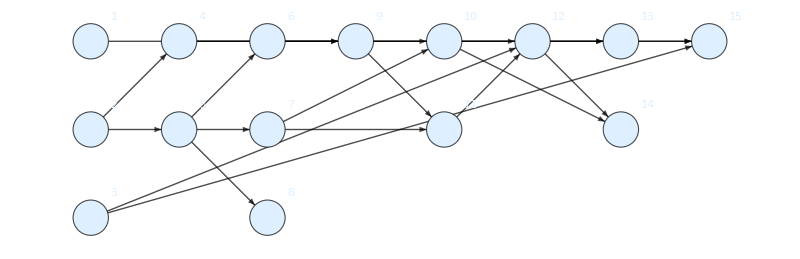

```mathematica
Graph[edges,VertexCoordinates->coordRules,VertexLabels->"Name",VertexSize->0.4,VertexStyle->LightBlue,EdgeStyle->Black,ImageSize->800]
```

```mathematica
coordRules
```

{1→{1,-1},2→{1,-2},3→{1,-3},4→{2,-1},5→{2,-2},6→{3,-1},7→{3,-2},8→{3,-3},9→{4,-1},10→{5,-1},11→{5,-2},12→{6,-1},13→{7,-1},14→{7,-2},15→{8,-1}}

```mathematica
ResourceFunction["GraphElementData"]
```

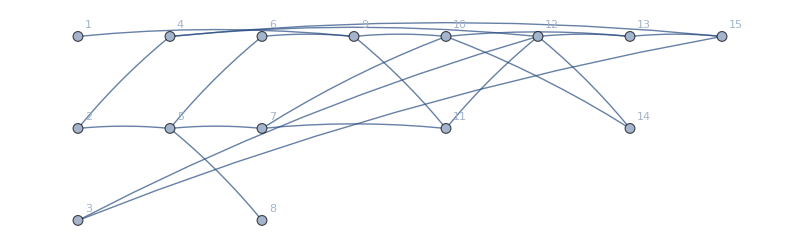

```mathematica
Graph[edges,
VertexLabels->"Name",
VertexCoordinates->coordRules,
EdgeShapeFunction->[{"CurvedArc","Curvature"->0.1}],
ImageSize->800]
```

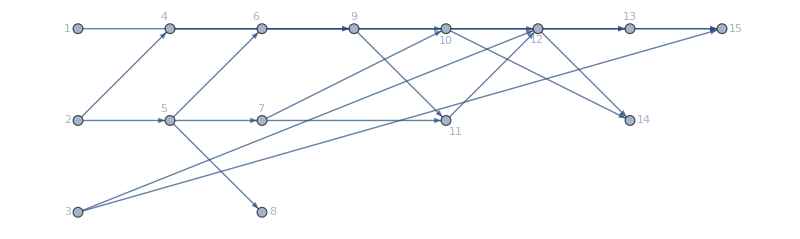

```mathematica
LayeredGraphPlot[edges,Left,
VertexLabels->"Name",
VertexCoordinates->coordRules,
ImageSize->800]
```

```mathematica
(*Функция для расчета времени начала работ*)
calculateStartTimes[data_]:=Module[{startTimes=<||>},(*Начальные работы*)Do[If[data[[i,3]]==={},startTimes[i]=0,startTimes[i]=Undefined],{i,Length[data]}];
(*Итеративное вычисление*)While[MemberQ[Values[startTimes],Undefined],Do[If[startTimes[i]===Undefined,predecessors=data[[i,3]];
If[AllTrue[predecessors,(NumericQ[startTimes[#]]&&startTimes[#]>=0)&],startTimes[i]=Max[Table[startTimes[p]+data[[p,2]],{p,predecessors}]]]],{i,Length[data]}]];
startTimes];

startTimes=calculateStartTimes[data];

(*Создаем данные для TimelinePlot*)
ganttData=Table[Callout[Interval[{startTimes[i],startTimes[i]+data[[i,2]]}],Row[{"№",i}],Before],{i,Length[data]}];

(*Строим диаграмму Ганта*)
TimelinePlot[ganttData,PlotLayout->"Stacked",PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,AxesLabel->{"Время","Работы"},PlotLabel->"Диаграмма Ганта",AspectRatio->1/2,ImageSize->800]
```

-Graphics-

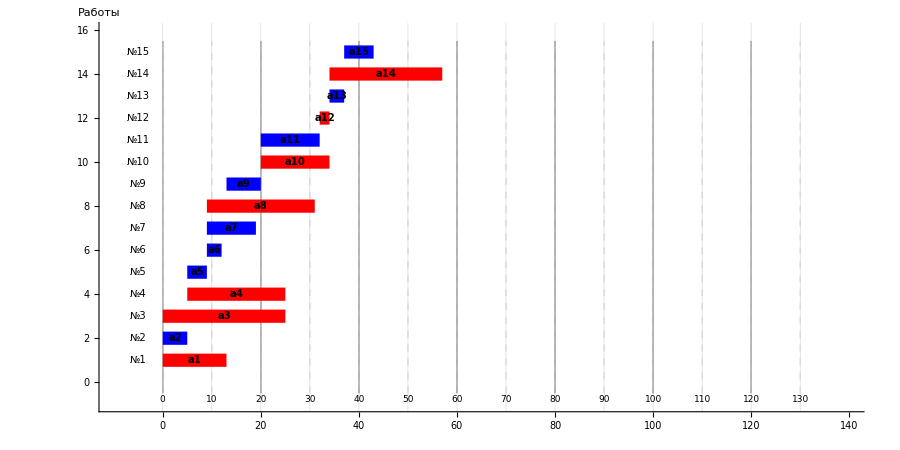

```mathematica
(*Функция расчета времени начала*)
calculateStartTimes[data_]:=Module[{startTimes=<||>},Do[If[data[[i,3]]==={},startTimes[i]=0,startTimes[i]=Undefined],{i,Length[data]}];
While[MemberQ[Values[startTimes],Undefined],Do[If[startTimes[i]===Undefined,predecessors=data[[i,3]];
If[AllTrue[predecessors,(NumericQ[startTimes[#]]&&startTimes[#]>=0)&],startTimes[i]=Max[Table[startTimes[p]+data[[p,2]],{p,predecessors}]]]],{i,Length[data]}]];
startTimes];

startTimes=calculateStartTimes[data];

(*Создаем классическую диаграмму Ганта*)
Graphics[{(*Сетка*){LightGray,Dashed,Table[Line[{{t,-0.5},{t,Length[data]+0.5}}],{t,0,130,10}]},{Gray,Table[Line[{{t,-0.5},{t,Length[data]+0.5}}],{t,0,130,20}]},(*Работы (полоски)*)Table[{(*Критический путь можно выделить другим цветом*)If[MemberQ[{1,3,4,8,10,12,14},i],Red,Blue],Rectangle[{startTimes[i],i-0.3},{startTimes[i]+data[[i,2]],i+0.3}],Black,Text[Style[Row[{"a",i}],10,Bold],{startTimes[i]+data[[i,2]]/2,i}]},{i,Length[data]}],(*Шкала времени внизу*)Table[Text[Style[t,9],{t,-0.8}],{t,0,130,10}],(*Номера работ слева*)Table[Text[Style[Row[{"№",i}],10],{-5,i}],{i,Length[data]}]},(*Настройки отображения*)PlotRange->{{-10,140},{-1,Length[data]+1}},AspectRatio->1/2,ImageSize->900,Axes->{True,False},AxesStyle->Black,AxesLabel->{None,"Работы"},GridLines->{Range[0,130,10],None},GridLinesStyle->LightGray]
```

```mathematica
ranks
```

{1→1,2→1,3→1,4→2,5→2,6→3,7→3,8→3,9→4,10→5,11→5,12→6,13→7,14→7,15→8}

```mathematica
(*Подготовка данных*)
vertices=ranks⟦All,1⟧
xPositions=Association[ranks](*Фиксированные X*)
yPositions=Association@Table[v->v,{v,vertices}] (*Начальные Y*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

<|1→1,2→1,3→1,4→2,5→2,6→3,7→3,8→3,9→4,10→5,11→5,12→6,13→7,14→7,15→8|>

<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10,11→11,12→12,13→13,14→14,15→15|>

```mathematica
Table[{xPositions[v],yPositions[v]},{v,vertices}]
```

{{1,1.},{1,1.81},{1,3.},{2,4.},{2,5.},{3,6.},{3,0.62},{3,8.},{4,9.},{5,10.},{5,11.},{6,12.},{7,13.},{7,14.},{8,15.}}

```mathematica
(*Создаем LocatorPane для управления Y-координатами*)
DynamicModule[{},Column[{LocatorPane[Dynamic[Table[{xPositions[v],yPositions[v]},{v,vertices}],(Do[yPositions[vertices[[i]]]=#[[i,2]],{i,Length[#]}])&],Dynamic@Graph[
edges,
VertexCoordinates->Table[{xPositions[v],yPositions[v]},{v,vertices}],
VertexLabels->"Name",
VertexSize->0.3,
VertexStyle->LightBlue,
EdgeStyle->Black,
PlotRange->{{-1,9},{0,16}},
ImageSize->800,
GridLines->{Range[-1,9,1],Automatic},
GridLinesStyle->LightGray],
LocatorAutoCreate->False],
Button["Сбросить Y",Do[yPositions[v]=v,{v,vertices}]
]}]]
```